1

InterpolatingFunction::dmval: Input value {-1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

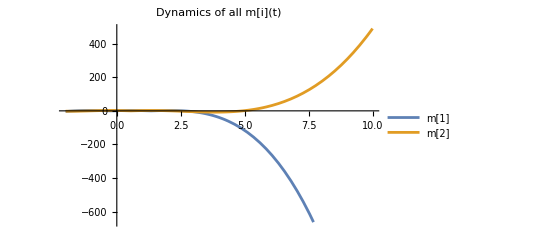

InterpolatingFunction::dmval: Input value {-1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

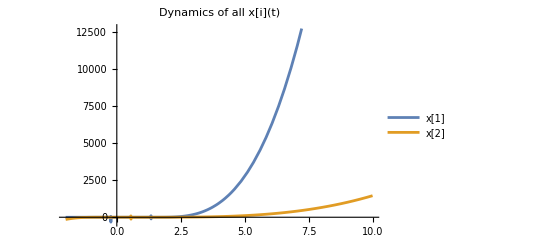

InterpolatingFunction::dmval: Input value {-1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

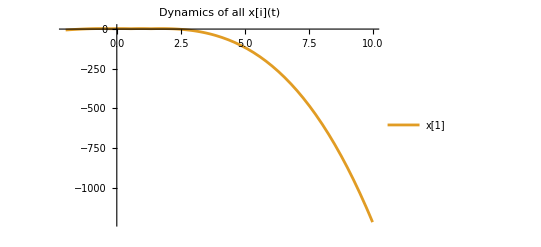

InterpolatingFunction::dmval: Input value {-1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

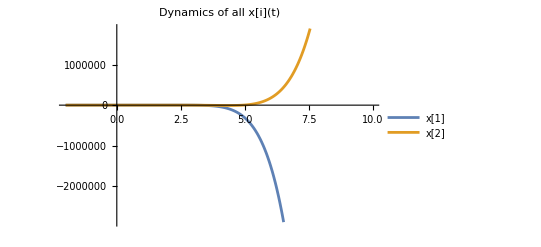

InterpolatingFunction::dmval: Input value {-1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

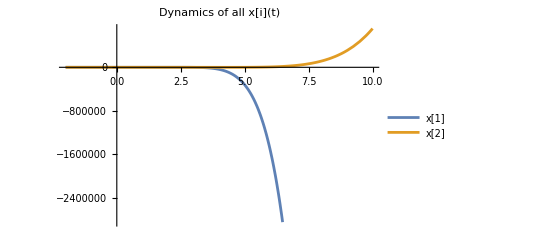

InterpolatingFunction::dmval: Input value {-1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

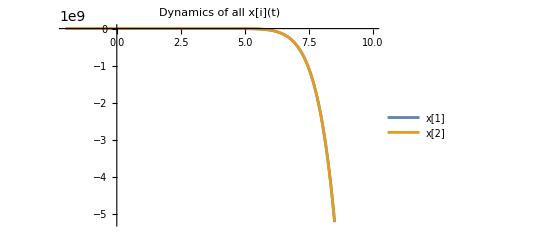

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(*Define the system of equations*)
u[k_,t_]:=Apply[Plus,Table[m[j][t](x[j][t]-x[k][t])Sign[j-k],{j,1,n}]]
u[k_,t_]:=Apply[Plus,Table[m[j][t](Exp[-Abs[x[k][t]-x[j][t]]]),{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[m[j][t]Sign[k-j],{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[m[j][t]Sign[k-j]Exp[-Abs[x[k][t]-x[j][t]]],{j,1,n}]]

(*Define the number of equations*)
n=2; (*Example for n=5*)

(*Define initial conditions*)
initialConditions=Flatten[Table[{m[i][0]==RandomReal[{1,10}],x[i][0]==RandomReal[{1,10}]},{i,n}]];
initialConditions={
m[1][0]==1,x[1][0]==3,
m[2][0]==2,x[2][0]==0
};

(*Define the system of ODEs*)
eqns=Flatten[Table[{
m[i]'[t]==-m[i][t]ux[i,t],
x[i]'[t]==u[i,t]},
{i,n}
]];

(*Solve the system numerically*)
Tstart=-2;
Tend=10;
T={t,Tstart,Tend};
sol2=NDSolve[Join[eqns,initialConditions],Flatten[Table[{m[i],x[i]},{i,n}]],T];


1
(*Plot all m[i]'s together*)plotM=Plot[Evaluate[Table[m[i][t]/. sol,{i,n}]],T,PlotLegends->Table["m["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all m[i](t)",PlotStyle->Array[ColorData[97],n]]

(*Plot all x[i]'s together*)
plotX=Plot[Evaluate[Table[x[i][t]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

plotX=Plot[Evaluate[Table[m[1][t]+m[2][t]/. sol,{i,1,1}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

Plot[Evaluate[Table[m[i][t]Abs[x[i][t]-x[Mod[i,n]+1][t]]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]


Plot[Evaluate[Table[m[i][t]x[i][t]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

Plot[Evaluate[Table[m[i][t]m[Mod[i,n]+1][t]Abs[x[i][t]-x[Mod[i,n]+1][t]]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

(*Display the plots*)
GraphicsColumn[{plotM,plotX}];
x[1][Tend]/.sol[[1]];
x[2][Tstart]/.sol[[1]];
```

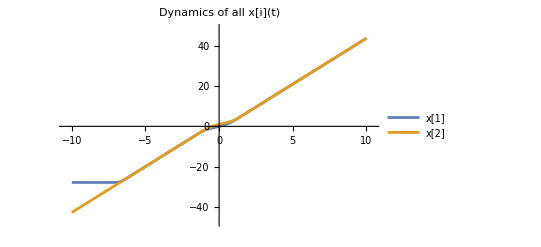

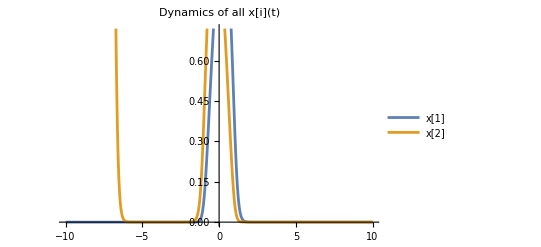

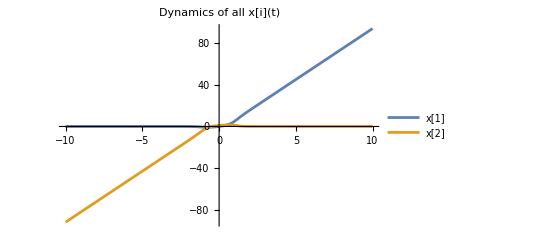

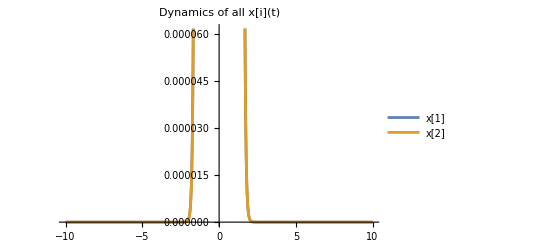

```mathematica
M1=(m[1][0]m[2][0](x[2][0]-x[1][0])+m[1][0]m[3][0](x[3][0]-x[1][0])+m[2][0]m[3][0](x[3][0]-x[2][0]))/.sol[[1]]
M2=(m[1][0]m[2][0]m[3][0])^2(x[2][0]-x[1][0])(x[3][0]-x[1][0])(x[3][0]-x[2][0])/.sol[[1]]
A1=m[1][0]^2(M1+2m[2][0]m[3][0](x[3][0]-x[2][0]));
A2=m[2][0]^2(M1+2m[1][0]m[3][0](x[3][0]-x[1][0]));
A3=m[3][0]^2(M1+2m[1][0]m[2][0](x[2][0]-x[1][0]));
M3=(A1 x[1][0]^0+A2 x[2][0]^0+A3 x[2][0]^0)/.sol[[1]]
M3=(A1 x[1][0]^1+A2 x[2][0]^1+A3 x[2][0]^1)/.sol[[1]]
M3=(A1 x[1][0]^2+A2 x[2][0]^2+A3 x[2][0]^2)/.sol[[1]]
```

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(m[1][0])^2 (m[2][0])^2 (m[3][0])^2 (-x[1][0]+x[2][0]) (-x[1][0]+x[3][0]) (-x[2][0]+x[3][0])/.sol⟦1⟧

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(m[3][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[2][0] (-x[1][0]+x[2][0]))+(m[2][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[3][0] (-x[1][0]+x[3][0]))+(m[1][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[2][0] m[3][0] (-x[2][0]+x[3][0]))/.sol⟦1⟧

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(m[3][0])^2 x[2][0] ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[2][0] (-x[1][0]+x[2][0]))+(m[2][0])^2 x[2][0] ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[3][0] (-x[1][0]+x[3][0]))+(m[1][0])^2 x[1][0] ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[2][0] m[3][0] (-x[2][0]+x[3][0]))/.sol⟦1⟧

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(m[3][0])^2 (x[2][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[2][0] (-x[1][0]+x[2][0]))+(m[2][0])^2 (x[2][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[3][0] (-x[1][0]+x[3][0]))+(m[1][0])^2 (x[1][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[2][0] m[3][0] (-x[2][0]+x[3][0]))/.sol⟦1⟧